```mathematica
mcSim[β_,j_,n_,iter_]:=Module[{grid=Array[1&,{n,n}],x,y,r,diff,a,rejected=0},grids=Array[{}&,iter];
For[k=1,k≤iter,k++,
For[l=1,l≤n^2,l++,               (*sweep*)
x=RandomInteger[{1,n}];y=RandomInteger[{1,n}];diff=2*j*grid[[x,y]]*(grid[[Mod[x+1,n,1],y]]+grid[[Mod[x-1,n,1],y]]+grid[[x,Mod[y+1,n,1]]]+grid[[x,Mod[y-1,n,1]]]);
a=If[diff>0,Exp[-β*diff],1];
r=RandomReal[];
If[a>r,grid[[x,y]]=-grid[[x,y]],rejected++];
];
grids[[k]]=grid
];
(*Print[rejected];*)
grids
]
magnetization[grids_,n_]:=1/(n^2*Dimensions[grids][[1]])*Total[Flatten[grids]]
magnetizationSq[grids_,n_]:=1/(Dimensions[grids][[1]])*Total[Flatten[Table[(1/n^2*Total[Flatten[grids[[i]]]])^2,{i,1,Dimensions[grids][[1]]}]]]
suscept[mag_,magSq_,β_]:=β*(magSq-mag^2)
energy[grids_,j_]:=Module[{grid,n,x,y,i},
sum=0;
n=Dimensions[grids[[1]]][[1]];
For[i=1,i≤Dimensions[grids][[1]],i++,
grid=grids[[i]];
For[x=1,x≤n,x++,
For[y=1,y≤n,y++,
sum=sum-j*grid[[x,y]]*(grid[[Mod[x+1,n,1],y]]+grid[[Mod[x-1,n,1],y]]+grid[[x,Mod[y+1,n,1]]]+grid[[x,Mod[y-1,n,1]]]);
];
];
];
sum/(2*Dimensions[grids][[1]])   (*   faktor 1/2: jedes paar wird sonst doppelt gezählt*)
]
energySq[grids_,j_]:=Module[{grid,n,sum1,x,y,i},
sum=0;
n=Dimensions[grids[[1]]][[1]];
For[i=1,i≤Dimensions[grids][[1]],i++,
grid=grids[[i]];
sum1=0;
For[x=1,x≤n,x++,
For[y=1,y≤n,y++,
sum1=sum1-(j*grid[[x,y]]*(grid[[Mod[x+1,n,1],y]]+grid[[Mod[x-1,n,1],y]]+grid[[x,Mod[y+1,n,1]]]+grid[[x,Mod[y-1,n,1]]]));
];
];
sum = sum + sum1^2/4;
];
sum/Dimensions[grids][[1]]
]
specificHeat[energy_,energySq_,β_]:=β^2*(energySq-energy^2)
magAntiferro[grids_]:=Module[{grid,n,i,x,y},
m=0;
n=Dimensions[grids[[1]]][[1]];
For[i=1,i≤Dimensions[grids][[1]],i++,
grid=grids[[i]];
For[x=1,x≤n,x++,
For[y=1,y≤n,y++,
m=m+(-1)^(x+y)*grid[[x,y]];
];
];
];
m/(Dimensions[grids][[1]]*n^2)
]
magAntiferroSq[grids_]:=Module[{grid,n,m1,i,x,y},
m=0;
n=Dimensions[grids[[1]]][[1]];
For[i=1,i≤Dimensions[grids][[1]],i++,
grid=grids[[i]];
m1=0;
For[x=1,x≤n,x++,
For[y=1,y≤n,y++,
m1=m1+(-1)^(x+y)*grid[[x,y]];
];
];
m=m+m1^2/n^2;
];
m/Dimensions[grids][[1]]
]
```

717.55428

p1

p2

$Aborted

Part::partd: Part specification heats ⟦ 1 ⟧ is longer than depth of object.

heats⟦1⟧

p3

Part::partd: Part specification heats ⟦ 2 ⟧ is longer than depth of object.

Part::partw: Part 3 of heats ⟦ 2 ⟧ does not exist.

Part::partw: Part 4 of heats ⟦ 2 ⟧ does not exist.

Part::partw: Part 5 of heats ⟦ 2 ⟧ does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

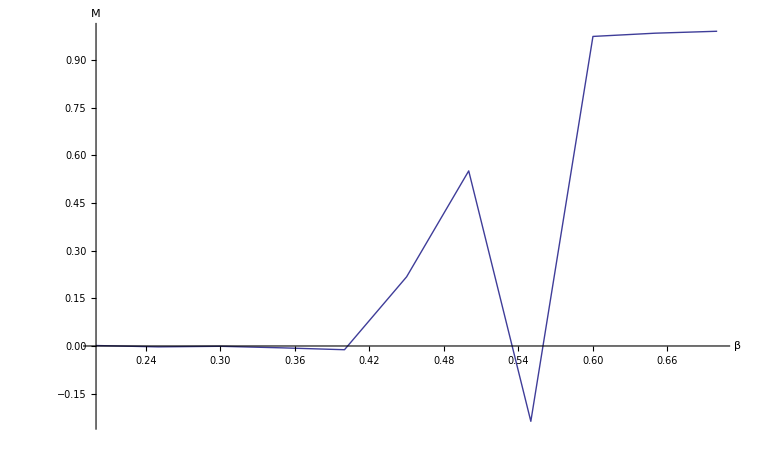

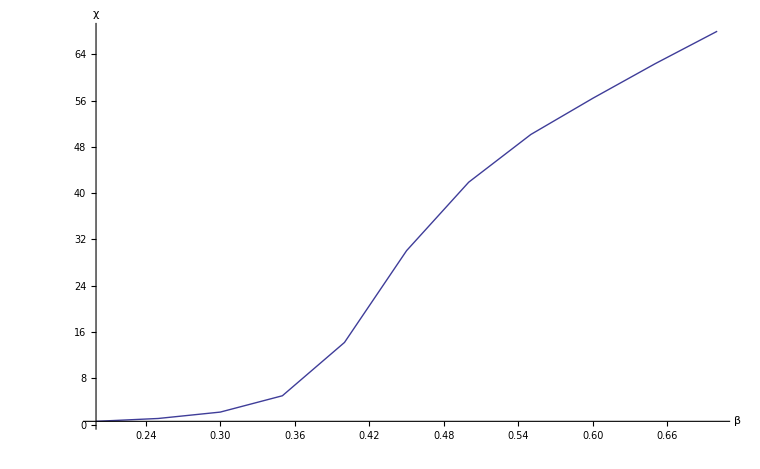

-Graphics-

```mathematica
n=10;j=-1;steps=100000;
βs=Table[β,{β,0.2,0.7,0.05}];
s=AbsoluteTiming[Parallelize[Table[mcSim[βs[[i]],j,n,steps],{i,1,Dimensions[βs][[1]]}]]];
s[[1]]
simβvar=s[[2]];
simβvar=simβvar[[All,10001;;-1]];
ms=Parallelize[Table[magAntiferro[simβvar[[i]]],{i,1,Dimensions[simβvar][[1]]}]];
Print["p1"]
p1=Table[{βs[[i]],ms[[i]]},{i,1,Dimensions[βs][[1]]}];
(*ListLinePlot[p1,PlotRange->All]*)
suscepts=Parallelize[Table[suscept[ms[[i]],magAntiferroSq[simβvar[[i]]],βs[[i]]],{i,1,Dimensions[simβvar][[1]]}]];
Print["p2"]
p2=Table[{βs[[i]],suscepts[[i]]},{i,1,Dimensions[βs][[1]]}];
(*ListLinePlot[p2,PlotRange->All]*)
heats=AbsoluteTiming[Parallelize[Table[specificHeat[energy[simβvar[[k]],j],energySq[simβvar[[k]],j],βs[[k]]],{k,1,Dimensions[βs][[1]]}]]];
heats[[1]]
Print["p3"]
p3=Table[{βs[[i]],heats[[2]][[i]]},{i,1,Dimensions[βs][[1]]}];
(*ListLinePlot[p3,PlotRange->All]*)
ListLinePlot[p1,PlotRange->All,AxesLabel->{β,M}]
ListLinePlot[p2,PlotRange->All,AxesLabel->{β,χ}]
ListLinePlot[p3,PlotRange->All,AxesLabel->{β,Subscript[C, V]}]
```

```mathematica
n=20;j=1;steps=100000;
βs=Table[β,{β,0.0,0.7,0.05}];
s=AbsoluteTiming[Parallelize[Table[mcSim[βs[[i]],j,n,steps],{i,1,Dimensions[βs][[1]]}]]];
s[[1]]
simβvar=s[[2]];
simβvar=simβvar[[All,5001;;-1]];
ms=Parallelize[Table[magnetization[simβvar[[i]],n],{i,1,Dimensions[simβvar][[1]]}]];
p1=Table[{βs[[i]],ms[[i]]},{i,1,Dimensions[βs][[1]]}];
ListLinePlot[p1,PlotRange->All]
suscepts=Parallelize[Table[suscept[ms[[i]],magnetizationSq[simβvar[[i]],n],βs[[i]]],{i,1,Dimensions[simβvar][[1]]}]];
p2=Table[{βs[[i]],suscepts[[i]]},{i,1,Dimensions[βs][[1]]}];
ListLinePlot[p2,PlotRange->All]
heats=Parallelize[Table[specificHeat[energy[simβvar[[k]],j],energySq[simβvar[[k]],j],βs[[k]]],{k,1,Dimensions[βs][[1]]}]];
p3=Table[{βs[[i]],heats[[i]]},{i,1,Dimensions[βs][[1]]}];
ListLinePlot[p3,PlotRange->All]
```

3333.70363

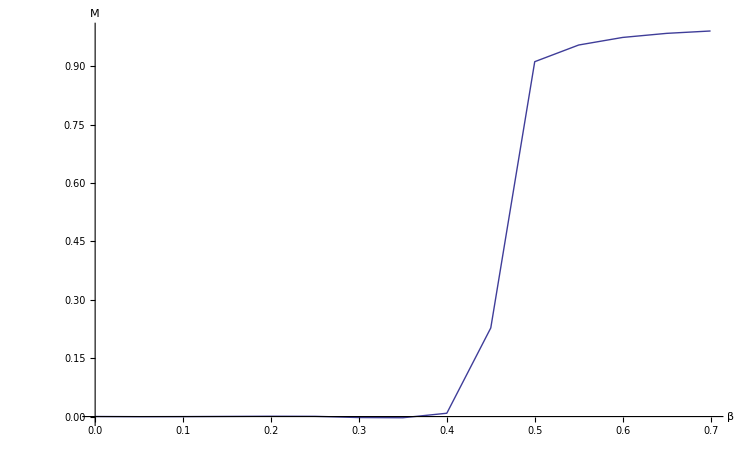

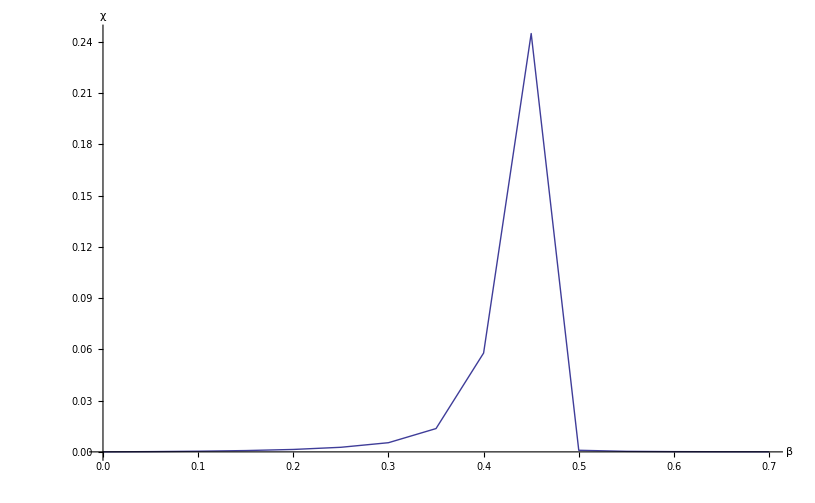

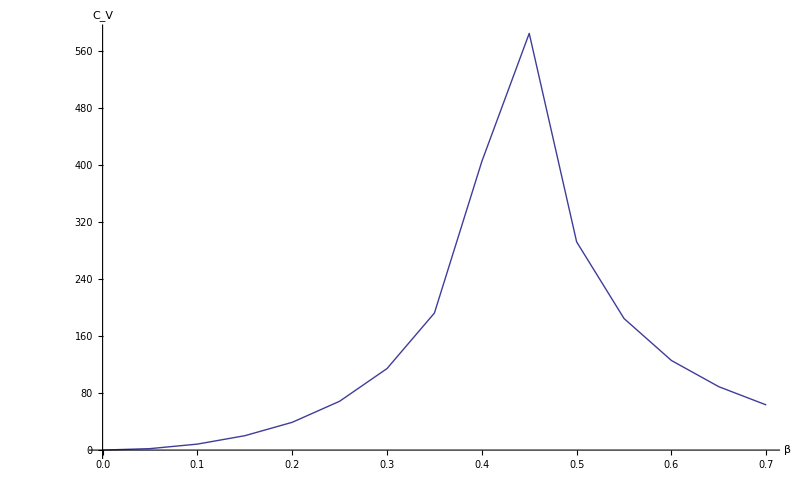

```mathematica
ListLinePlot[p1,PlotRange->All,AxesLabel->{β,M}]
ListLinePlot[p2,PlotRange->All,AxesLabel->{β,χ}]
ListLinePlot[p3,PlotRange->All,AxesLabel->{β,Subscript[C, V]}]
```

```mathematica
1/2.269//N
```

0.440723

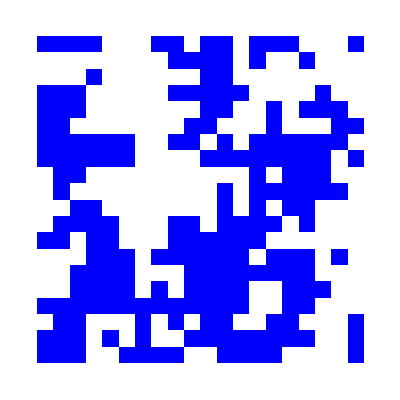
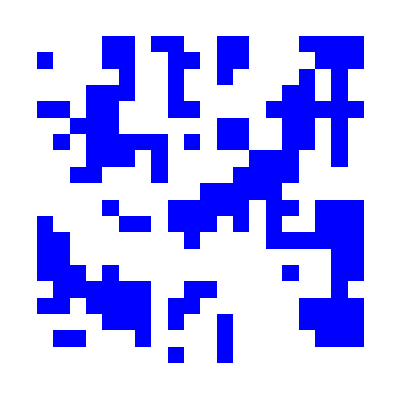
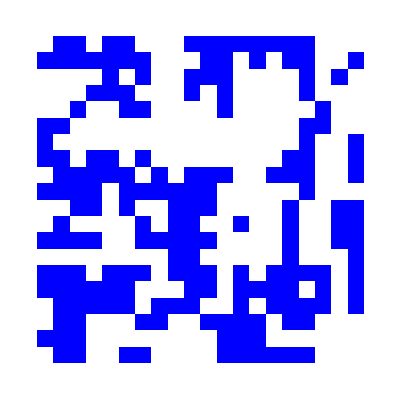
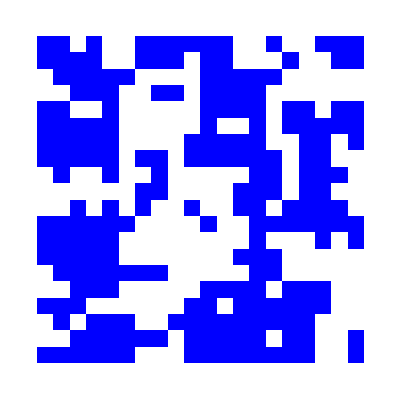
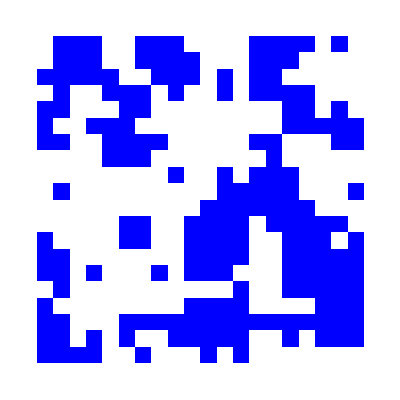
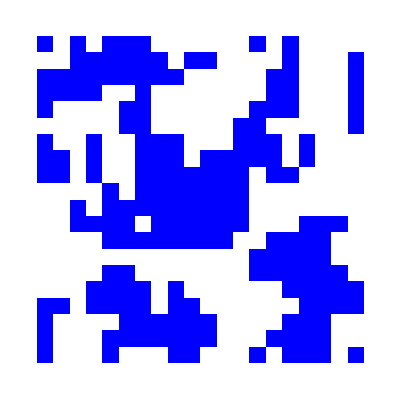
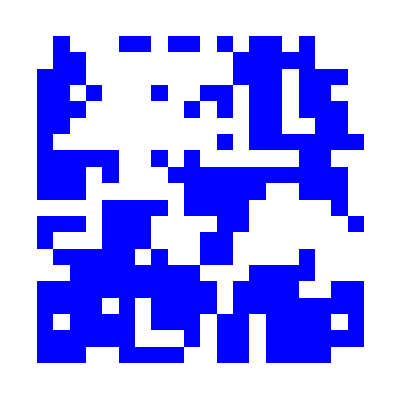
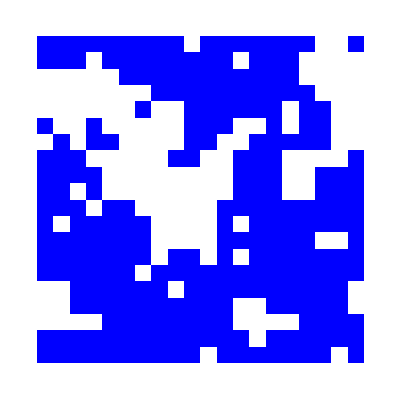

```mathematica
βs=Table[β,{β,0.24,0.5,0.02}];
nr=3111;
simβvar=Parallelize[Table[mcSim[βs[[i]],1,20,nr],{i,1,Dimensions[βs][[1]]}]];
Table[ArrayPlot[simβvar[[i*1,nr]],ColorRules->{1->Blue,-1->White}],{i,1,Dimensions[βs][[1]]}]
```

```mathematica
β=1;
j=1;
n=10;
iter=1000;
dauer=AbsoluteTiming[mcSim[β,j,n,iter]];
dauer[[1]]
```

17.65402

```mathematica
com=Compile[{β,j,n,iter},mcSim[β,j,n,iter]];           (*bringt fast nichts*)
dauer1=AbsoluteTiming[mcSim[β,j,n,iter]];
dauer1[[1]]
```

17.67202

```mathematica
ByteCount[dauer[[2]]]
```

29280080

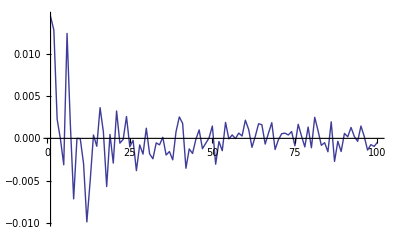

```mathematica
β=0;
j=1;
n=10;
maxiter=10000;
anzahl=100;
plt=Parallelize[Table[magnetization[mcSim[β,j,n,maxiter/anzahl*i],n],{i,1,anzahl}]];
ListLinePlot[plt,PlotRange->All]
```